```mathematica
Plot[{(Sqrt[(2/Pi)](Sin[Pi Log[x]]/x^2)),(Sqrt[(2/Pi)](Sin[2 Pi Log[x]]/x^2)), (Sqrt[(2/Pi)](Sin[3 Pi Log[x]]/x^2)), (Sqrt[(2/Pi)](Sin[4 Pi Log[x]]/x^2))},{x,1,2.71828},PlotStyle->{Blue, {Red, Dashed},{Darker[Green], Dotted}, {Magenta,DotDashed}}, PlotLabels->{Subscript[λ,"1"]}]
```

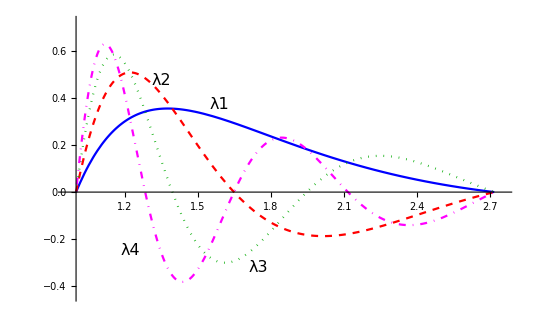

```mathematica
f[x_]:= 4 +x^2 Pi^2;
puntos={1,2,3,4};
N[Map[f,puntos]]
```

{13.8696,43.4784,92.8264,161.914}